# BergNet: Classifying Harvard Dining Hall Food Using Deep Learning

## Linda Zeng Harvard University Pre-College Program Presented on August 2, 2024 | Revised on September 29, 2024 Contact: 26lindaz@students.harker.org Keywords: Food Classification, Neural Networks, Machine Learning

## Motivation

Annenberg Hall, known as “The Hogwarts of Harvard,” is Harvard’s iconic first-year dining facility, spanning 88,000 square feet. During my four weeks in the Pre-College Program, it became a central part of my daily routine. With its unique architecture and vibrant atmosphere, Annenberg plays a significant role in shaping the undergraduate and summer student experience.

In this project, I explore the potential of training a neural network to analyze and recognize the food served at Annenberg Hall. Leveraging machine learning techniques, I aim to assess how well a model can classify images of the diverse meals provided in the dining hall. This study not only serves as a fun and practical application but also introduces broader implications for machine learning in food analysis—ranging from nutrition recommendation and meal balancing to improving food monitoring in industries. This notebook serves as a guide through my experiments.

## Data Collection

First, I collected images by visiting the dining hall on Wednesday, July 31, 2024 during lunch and dinner and capturing a total of 67 photographs of various food items. Each image was labeled into one of the following categories: “Vegetable,” “Grains,” “Soup,” “Fruit,” and “Protein.” This labeling process is crucial, as it allows me to create a structured dataset that the neural network can learn from.

Given that this project is novel, I faced the challenge of working with a limited dataset that I had to collect myself. Data scarcity is a significant concern in the field of machine learning, as having a restricted number of examples can hinder a model’s ability to generalize and accurately classify unseen data. To address this issue, I will employ data augmentation techniques and explore additional strategies to enhance ny dataset, ensuring that my neural network can effectively learn to recognize the diverse array of food served at Annenberg Hall.

### To use pre-made train and test sets, run this cell:

```mathematica
currentDirectory=ToString[NotebookDirectory[]];
trainingSet = Get[currentDirectory<>"data/train-set.mx"]
testSet = Get[currentDirectory<>"data/test-set.mx"]
```

### To load in data into your own train and test sets, proceed below:

#### Find your Current Directory

```mathematica
currentDirectory=ToString[NotebookDirectory[]];
```

#### Loading in Data

This cell may take a moment to finish running.

```mathematica
(*Define data labels and paths*)data={{"IMG_3460.HEIC","Grains","Rice"},{"IMG_3461.HEIC","Protein","Tofu"},{"IMG_3462.HEIC","Protein","Chicken"},{"IMG_3463.HEIC","Protein","Pulled Chicken"},{"IMG_3464.HEIC","Protein","Tofu"},{"IMG_3465.HEIC","Vegetable","Carrot"},{"IMG_3466.HEIC","Soup","Green Curry"},{"IMG_3467.HEIC","Protein","Fried Chicken"},{"IMG_3468.HEIC","Grains","Tater Tots"},{"IMG_3469.HEIC","Vegetable","Green Beans"},{"IMG_3470.HEIC","Grains","Pizza"},{"IMG_3471.HEIC","Vegetable","Lima Beans"},{"IMG_3472.HEIC","Vegetable","Broccoli"},{"IMG_3473.HEIC","Protein","Sausage"},{"IMG_3474.HEIC","Soup","Tomato Basil Soup"},{"IMG_3475.HEIC","Soup","Chicken Tortilla Soup"},{"IMG_6164.HEIC","Vegetable","Spring Mix"},{"IMG_6165.HEIC","Vegetable","Baby Arugula"},{"IMG_6166.HEIC","Vegetable","Lettuce"},{"IMG_6167.HEIC","Vegetable","Spinach"},{"IMG_6168.HEIC","Protein","Tuna"},{"IMG_6169.HEIC","Soup","Parmesan Shredded Cheese"},{"IMG_6170.HEIC","Protein","Chicken"},{"IMG_6171.HEIC","Soup","Cheese"},{"IMG_6172.HEIC","Grains","NA"},{"IMG_6173.HEIC","Grains","NA"},{"IMG_6174.HEIC","Grains","NA"},{"IMG_6175.HEIC","Grains","Quinoa"},{"IMG_6176.HEIC","Fruit","Tomato"},{"IMG_6177.HEIC","Vegetable","Corn"},{"IMG_6178.HEIC","Vegetable","Carrot"},{"IMG_6181.HEIC","Soup","Yogurt"},{"IMG_6182.HEIC","Fruit","Avocado"},{"IMG_6183.HEIC","Fruit","Olive"},{"IMG_6184.HEIC","Fruit","Jalapenos"},{"IMG_6185.HEIC","Vegetable","garlic"},{"IMG_6186.HEIC","Vegetable","Onion"},{"IMG_6187.HEIC","Grains","NA"},{"IMG_6188.HEIC","Soup","Hummus"},{"IMG_6189.HEIC","Grains","Croutons"},{"IMG_6190.HEIC","Soup","Ketchup"},{"IMG_6191.HEIC","Protein","Tofu"},{"IMG_6192.HEIC","Vegetable","Edamame"},{"IMG_6193.HEIC","Protein","Egg"},{"IMG_6194.HEIC","Vegetable","Chickpea"},{"IMG_6195.HEIC","Vegetable","Pepper"},{"IMG_6196.HEIC","Grains","Pasta"},{"IMG_6213.HEIC","Grains","Cookies"},{"IMG_6214.HEIC","Fruit","Orange"},{"IMG_6215.HEIC","Fruit","Apple"},{"IMG_6216.HEIC","Fruit","Pear"},{"IMG_6217.HEIC","Fruit","Banana"},{"IMG_6262.HEIC","Grains","Potatoes"},{"IMG_6263.HEIC","Grains","Sweet Potatoes"},{"IMG_6264.HEIC","Protein","Bacon"},{"IMG_6265.HEIC","Soup","Cheese"},{"IMG_6266.HEIC","Soup","Sour Cream"},{"IMG_6267.HEIC","Soup","Salsa"},{"IMG_6268.HEIC","Fruit","Pineapple"},{"IMG_6269.HEIC","Grains","Cookies"},{"IMG_6270.HEIC","Grains","Pasta"},{"IMG_6271.HEIC","Soup","Pesto Sauce"},{"IMG_6272.HEIC","Soup","Marinara Sauce"},{"IMG_6273.HEIC","Vegetable","Spinach"},{"IMG_6274.HEIC","Vegetable","Eggplant"},{"IMG_6275.HEIC","Protein","Fish"},{"IMG_6276.HEIC","Protein","Pork"}};
paths=data[[All,1]];
imagedirectory=currentDirectory<>"data/raw-data-wednesday/";
fullPaths=FileNameJoin[{imagedirectory,#}]&/@paths;
(*load in images*)
images=Import/@fullPaths;
(*resize images to 224 by 224*)
resizedimages=ImageResize[#,{224,224}]&/@images;
(*add images to data label and path matrix*)
newMatrix=Transpose[Join[Transpose[data],{resizedimages}]];
```

#### Splitting into Train and Test Data

```mathematica
(*Set the seed for reproducibility*)
SeedRandom[1234];
(*Define the train-test split ratio*)
trainRatio=0.7;

(*Separate data by category*)
categoryData=GroupBy[newMatrix,#[[2]]&];

(*Initialize empty lists for training and testing sets*)
trainingSet={};
testSet={};

(*Process each category*)
Do[(*Extract data for the current category*)
currentCategoryData=categoryData[category];
(*Shuffle the data*)
shuffledCategoryData=RandomSample[currentCategoryData];
(*Calculate the number of training samples*)
numCategorySamples=Length[shuffledCategoryData];
numTrainSamples=Floor[trainRatio*numCategorySamples];
(*Split the data into training and testing sets*)
categoryTrainingSet=Take[shuffledCategoryData,numTrainSamples];
categoryTestSet=Drop[shuffledCategoryData,numTrainSamples];
(*Append to the global training and testing sets*)
trainingSet=Join[trainingSet,categoryTrainingSet];
testSet=Join[testSet,categoryTestSet],{category,Keys[categoryData]}];
```

#### Save your Train and Test Data

```mathematica
Save[currentDirectory<>"data/train-set-custom.mx",trainingSet]
Save[currentDirectory<>"data/test-set-custom.mx",testSet]
(*To reload them in: trainingSet = Get[currentDirectory<>"data/train-set-custom.mx"]*)
```

### Example of Data

```mathematica
randomSample=RandomSample[trainingSet,5];
Print["Length of Training Data: ",Length[trainingSet]];
Print["Length of Test Data: ",Length[testSet]];
Print["Random Sample of 5 Entries from Training Data: ",randomSample];
```

Length of Training Data: 45

Length of Test Data: 22

Random Sample of 5 Entries from Training Data: {{IMG_6269.HEIC,Grains,Cookies,-Graphics-},{IMG_6181.HEIC,Soup,Yogurt,-Graphics-},{IMG_6195.HEIC,Vegetable,Pepper,-Graphics-},{IMG_6175.HEIC,Grains,Quinoa,-Graphics-},{IMG_6217.HEIC,Fruit,Banana,-Graphics-}}

## Data Augmentation

To increase the amount of training data samples, I provide a series of transformations to each training data sample in the training set. These included flipping them both horizontally and vertically, cropping them to a size of 100 by 100 pixels, and rotating them at angles of 45, 135, 225, and 315 degrees, translating the images slightly to the left and right, adding various types of noise (including random, Gaussian, and Poisson noise), boosting their colors for greater vibrancy, and adjusting the color balance to enhance brightness while creating darker and lighter versions of each image.

### To use pre-made augmented training data, run this cell:

```mathematica
augmentedTrainingSet = Get[currentDirectory<>"data/augmented-train-set.mx"]
```

### To create your own augmented training set, proceed below:

#### Extract original images

```mathematica
originalImages=trainingSet[[All,4]]; 
augmentedImages={};
```

#### Define transformations

```mathematica
flippedHorizontally=ImageReflect[#,Left]&/@originalImages;
flippedVertically=ImageReflect[#]&/@originalImages;
croppedImages=ImageCrop[#,{100,100}]&/@originalImages;
rotatedImages=ImageRotate[#,45]&/@originalImages; (*Example rotation of 45 degrees*)
rotatedImages2=ImageRotate[#,135]&/@originalImages; (*Example rotation of 45 degrees*)
rotatedImages3=ImageRotate[#,225]&/@originalImages; (*Example rotation of 45 degrees*)
rotatedImages4=ImageRotate[#,315]&/@originalImages; (*Example rotation of 45 degrees*)
translatedImagesLeft=ImageTransformation[#,#+0.25&]&/@originalImages;
translatedImagesRight=ImageTransformation[#,#-0.25&]&/@originalImages;
noisyImages=ImageEffect[#,"Noise"]&/@originalImages;
noisyImages2=ImageEffect[#,"GaussianNoise"]&/@originalImages;
noisyImages3=ImageEffect[#,"PoissonNoise"]&/@originalImages;
boostedImages=ImageEffect[#,"ColorBoosting"]&/@originalImages;
recoloredImages =ImageAdjust[#,{1,0.5}]&/@originalImages;
darkerImages =Darker[#]&/@originalImages;
lighterImages=Lighter[#]&/@originalImages;
```

#### Generate augmented data for each transformation

```mathematica
createAugmentedData[images_]:=Transpose[{trainingSet[[All,1]],trainingSet[[All,2]],trainingSet[[All,3]],images}]
augmentedTrainingSet=Join[createAugmentedData[originalImages],
createAugmentedData[flippedHorizontally],
createAugmentedData[flippedVertically],
createAugmentedData[croppedImages],
createAugmentedData[rotatedImages],
createAugmentedData[rotatedImages2],
createAugmentedData[rotatedImages3],
createAugmentedData[rotatedImages4],
createAugmentedData[translatedImagesLeft],
createAugmentedData[translatedImagesRight],
createAugmentedData[noisyImages],
createAugmentedData[noisyImages2],
createAugmentedData[noisyImages3],
createAugmentedData[boostedImages],
createAugmentedData[darkerImages],
createAugmentedData[lighterImages],
createAugmentedData[recoloredImages]];
```

#### Save your augmented data

```mathematica
Save[currentDirectory<>"data/augmented-train-set-custom.mx",augmentedTrainingSet]
(*To reload them in: augmentedTrainingSet = Get[currentDirectory<>"data/augmented-train-set-custom.mx"]*)
```

### Example of Augmented Data

```mathematica
randomSample=RandomSample[augmentedTrainingSet,10];
Print["Length of Augmented Training Data: ",Length[augmentedTrainingSet]];
Print["Random Sample of 10 Entries from Augmented Training Data: ",randomSample];
```

Length of Augmented Training Data: 765

Random Sample of 10 Entries from Augmented Training Data: {{IMG_6263.HEIC,Grains,Sweet Potatoes,-Graphics-},{IMG_6270.HEIC,Grains,Pasta,-Graphics-},{IMG_6263.HEIC,Grains,Sweet Potatoes,-Graphics-},{IMG_6182.HEIC,Fruit,Avocado,-Graphics-},{IMG_6216.HEIC,Fruit,Pear,-Graphics-},{IMG_6186.HEIC,Vegetable,Onion,-Graphics-},{IMG_6181.HEIC,Soup,Yogurt,-Graphics-},{IMG_6190.HEIC,Soup,Ketchup,-Graphics-},{IMG_6186.HEIC,Vegetable,Onion,-Graphics-},{IMG_6178.HEIC,Vegetable,Carrot,-Graphics-}}

## Training a Custom Model with Data Augmentation Set

In this section, I focus on training our custom neural network model, (Annen)BergNet, using Mathematica’s NetChain functionality. BergNet consists of multiple layers, including two convolutional layers followed by ReLU activations and pooling layers, which help extract hierarchical features from input images. To prevent overfitting, U incorporate dropout layers wit ha value of 0.1. The network architecture transitions to fully connected layers to transfer the information learned from image features into the five classes. Through the softmax layer, each class receives a probability from the model, with the highest probability class being the model’s classification. 

The model is trained on our augmented training set, which includes both the original images and their transformed versions. By presenting the model with these varied inputs during training, it learns to recognize patterns and features that are invariant to these alterations, thereby improving its ability to generalize to unseen data. Once the training is complete, the model’s performance is evaluated on a held-out test set that was not used during the training phase. This test set serves as an unbiased measure of how well the model can generalize its learned knowledge to new, unseen examples. By comparing the model’s predictions on the test set with the actual labels, I assess its accuracy.

### Converting the data into input-output pairs

```mathematica
trainingData=Rule@@@augmentedTrainingSet[[All,{4,2}]];
testData=Rule@@@testSet[[All,{4,2}]];
```

### Defining and initializing neural network

I configure the input to be a 224 by 224 RGB image and the output to be our five classes. We define the layers in the model architecture and initialize random weights to begin with.

```mathematica
classes={"Vegetable","Grains","Soup","Fruit","Protein"};
bergEncoder=NetEncoder[{"Image",{224,224},"ColorSpace"->"RGB"}];
bergDecoder=NetDecoder[{"Class",classes}];
```

```mathematica
bergNet=NetChain[{ConvolutionLayer[16,{3,3}],
Ramp,
PoolingLayer[2,2],
DropoutLayer[0.1],

ConvolutionLayer[32,{3,3}],
Ramp,
PoolingLayer[2,2],
DropoutLayer[0.1],

FlattenLayer[],

LinearLayer[128],
Ramp,
LinearLayer[5],
SoftmaxLayer[]},

"Output"->bergDecoder,"Input"->bergEncoder];
```

You may press the + button below to view the neural network layers.

```mathematica
initializedBergNet=NetInitialize[bergNet]
```

NetChain[<13>]

### Baseline Results with No Training

Before training, I evaluate the model on both the training and test data to establish a “zero-shot” baseline, where the performance should be effectively random. This initial evaluation helps us quantify the improvements gained from training by providing a clear point of comparison.

```mathematica
(*Calculate accuracies*)zeroShotTrainAccuracy=NetMeasurements[initializedBergNet,trainingData,"Accuracy"];
zeroShotAccuracy=NetMeasurements[initializedBergNet,testData,"Accuracy"];

(*Print the results*)
Print["Train Data (Zero-shot) Accuracy: ",zeroShotTrainAccuracy];
Print["Test Data (Zero-Shot) Accuracy: ",zeroShotAccuracy];
```

Train Data (Zero-shot) Accuracy: 0.219608

Test Data (Zero-Shot) Accuracy: 0.181818

### Training the Custom Model

This step takes around 2-3 minutes. You may choose to load in an already trained version of this model that I have provided to save time.

#### To load in already trained BergNet:

```mathematica
trainedBergNet=Import[currentDirectory<>"models/trainedBergNet.mx"];
```

#### To train your own BergNet:

```mathematica
trainedBergNet=NetTrain[initializedBergNet,trainingData,ValidationSet->testData]
```

NetChain[<13>]

```mathematica
(*Saving the Model*)
Export[currentDirectory<>"models/trainedBergNetCustom.mx",trainedBergNet];
(*To reload: trainedBergNet=Import[currentDirectory<>"models/trainedBergNetCustom.mx"];*)
```

### Evaluation of BergNet

#### Accuracy Scores

```mathematica
(*Calculate and print the training accuracy*)
trainingBergAccuracy=NetMeasurements[trainedBergNet,trainingData,"Accuracy"];
Print["Training Accuracy: ",trainingBergAccuracy];

(*Calculate and print the test accuracy*)
bergAccuracy=NetMeasurements[trainedBergNet,testData,"Accuracy"];
Print["Test Accuracy: ",bergAccuracy];
```

Training Accuracy: 0.922876

Test Accuracy: 0.636364

```mathematica
ClassifierMeasurements[trainedBergNet,testData]
```

#### Examples of Predictions

```mathematica
(*Evaluate the model on the test data*)predictedLabels=trainedBergNet[Keys[testData]];
(*Get the actual labels from the test data*)actualLabels=Values[testData];

(*Get the images from the test data*)
testImages=Keys[testData];

(*Create a list of results with images,predicted labels,and actual labels*)
results=Transpose[{testImages,predictedLabels,actualLabels}];

(*Takes 5 random examples, REMOVE in order to see all results*)
limitedResults=RandomSample[results,5];

(*Display the results with images,predicted labels,and actual labels*)
Grid[Prepend[limitedResults,{"Image","Predicted Label","Actual Label"}],Frame->All,Spacings->{2,2}]
```

```mathematica
trainedBergNet[-Graphics-,{"TopProbabilities", 3}]
```

{Fruit→0.00475832,Soup→0.0133416,Grains→0.978145}

## Investigating Performance without Data Augmentation

In this section, I evaluate the impact of training our model without applying data augmentation techniques. Data augmentation typically helps improve the model’s generalization by introducing variability in the training set, simulating different conditions the model might encounter. To investigate the importance of augmentation, I train a version of our model, BergNet, solely on the original, not augmented training dataset.

### Converting the data into input-output pairs

```mathematica
originalTrainingData=Rule@@@trainingSet[[All,{4,2}]];
Print["Length of original training data:",Length[originalTrainingData]]
```

45

### Initializing Neural Network

```mathematica
initializedBergNetWithoutAug=NetInitialize[bergNet];
```

### Training the Custom Model

This step takes around 1-2 minutes. You may choose to load in an already trained version of this model that I have provided to save time.

#### To load in already trained BergNet without data augmentation:

```mathematica
trainedBergNetWithoutAug=Import[currentDirectory<>"models/trainedBergNetNoAug.mx"];
```

#### To train your own BergNet without data augmentation

```mathematica
trainedBergNetWithoutAug=NetTrain[initializedBergNetWithoutAug,originalTrainingData,ValidationSet->testData]
```

NetChain[<13>]

```mathematica
(*Saving the Model*)
Export[currentDirectory<>"models/trainedBergNetNoAugCustom.mx",trainedBergNet]
(*To reload: trainedBergNetWithoutAug=Import[currentDirectory<>"models/trainedBergNetNoAugCustom.mx"];*)
```

/Users/lindazeng/Documents/Harvard Summer School 2024 - Mathematical Elements of AI/BergNet/trainedBergNetNoAugCustom.mx

### Evaluation of BergNet without Data Augmentation

#### Accuracy Scores

```mathematica
(*Calculate and print the training accuracy without augmentation*)
noAugTrainingAccuracy=NetMeasurements[trainedBergNetWithoutAug,originalTrainingData,"Accuracy"];
Print["Training Accuracy without Data Augmentation: ",noAugTrainingAccuracy];

(*Calculate and print the test accuracy without augmentation*)
bergNoAugmentationAccuracy=NetMeasurements[trainedBergNetWithoutAug,testData,"Accuracy"];
Print["Test Accuracy without Data Augmentation: ",bergNoAugmentationAccuracy];
```

Training Accuracy without Data Augmentation: 0.955556

Test Accuracy without Data Augmentation: 0.454545

#### Example Predictions

```mathematica
(*Evaluate the model on the test data*)
predictedLabels=trainedBergNetWithoutAug[Keys[testData]];
(*Get the actual labels from the test data*)actualLabels=Values[testData];

(*Get the images from the test data*)
testImages=Keys[testData];

(*Create a list of results with images,predicted labels,and actual labels*)
results=Transpose[{testImages,predictedLabels,actualLabels}];

(*Take only 5 results*)limitedResults=RandomSample[results,5];

(*Display the results with images,predicted labels,and actual labels*)
Grid[Prepend[limitedResults,{"Image","Predicted Label","Actual Label"}],Frame->All,Spacings->{2,2}]
```

Image | Predicted Label | Actual Label
-Graphics- | Soup | Grains
-Graphics- | Vegetable | Vegetable
-Graphics- | Fruit | Fruit
-Graphics- | Soup | Grains
-Graphics- | Vegetable | Vegetable

## Fine-tuning a Pre-trained Model

Given the limited size of our dataset, fine-tuning a pre-trained model is often a more effective approach than training a custom model from scratch. Pre-trained models, such as EfficientNet, have already been trained on vast datasets like ImageNet, allowing them to learn general features that are useful for a wide variety of tasks. By fine-tuning, we leverage the knowledge these models have acquired and adapt it to our specific problem with a smaller amount of data. This method helps mitigate overfitting, which is a common risk when training models on limited data, as the pre-trained model starts with well-established weights that only need to be slightly adjusted. This results in faster convergence and often leads to better performance compared to training a custom model that starts from random initialization.

### Load in Pre-trained EfficientNet

```mathematica
pretrainedNet = NetModel["EfficientNet Trained on ImageNet"]
```

NetChain[<26>]

### Adjust the pre-trained model to our specific task input and output.

I take the weights, parameters, and layers for most of EfficientNet but adjust the final output linear layer and softmax to output five classes for our specific task. We also replace the input and output without custom encoder and decoders.

```mathematica
baseModel=NetTake[pretrainedNet,{1,24}]
```

NetChain[<24>]

```mathematica
(*Build the modified model*)
classes={"Vegetable","Grains","Soup","Fruit","Protein"};
bergEncoder=NetEncoder[{"Image",{224,224},"ColorSpace"->"RGB"}];
bergDecoder=NetDecoder[{"Class",classes}];
modifiedModel=NetChain[{baseModel,LinearLayer[5],SoftmaxLayer[]},"Input"->bergEncoder,"Output"->bergDecoder];
```

NetChain[<3>]

```mathematica
(*Initialize the model*)
initializedPretrainedNet=NetInitialize[modifiedModel]
```

NetChain[<3>]

### Baseline Results with No Training

Before training, I evaluate the model on both the training and test data to establish a baseline, where the performance should be effectively random. This initial evaluation helps us quantify the improvements gained from training by providing a clear point of comparison.

```mathematica
(*Measure accuracy on training and test data*)
trainPretrainedAccuracy=NetMeasurements[initializedPretrainedNet,trainingData,"Accuracy"];
zeroShotPretrainedAccuracy=NetMeasurements[initializedPretrainedNet,testData,"Accuracy"];

(*Print the results*)
Print["Zero-shot Accuracy on Train Data for EfficientNet: ",trainPretrainedAccuracy];
Print["Zero-shot Accuracy on Test Data for EfficientNet: ",zeroShotPretrainedAccuracy];
```

Zero-shot Accuracy on Train Data for EfficientNet: 0.222222

Zero-shot Accuracy on Test Data for EfficientNet: 0.136364

### Fine-tune the Pre-trained Model

Fine-tuning takes approximately 20 minutes. You may choose to load in an already fine-tuned version of this model that I have provided to save time.

#### To load in an already fine-tuned EfficientNet:

```mathematica
trainedPretrainedNet=Import[currentDirectory<>"models/trainedEfficientNet.mx"]
```

#### To fine-tune your own EfficientNet:

```mathematica
trainedPretrainedNet=NetTrain[initializedPretrainedNet,trainingData,"ValidationSet"->testData,"MaxTrainingRounds"->10,(*Adjust as needed*)"LearningRate"->0.001,(*Adjust learning rate as needed*)"BatchSize"->32 (*Adjust batch size as needed*)]
```

NetChain[<3>]

```mathematica
(*Saving the Model*)
Export[currentDirectory<>"models/trainedEfficientNetCustom.mx",trainedPretrainedNet];
(*To reload: trainedPretrainedNet=Import[currentDirectory<>"models/trainedEfficientNetCustom.mx"];*)
```

/Users/lindazeng/Documents/Harvard Summer School 2024 - Mathematical Elements of AI/BergNet/trainedEfficientNet.mx

### Evaluation of Fine-tuned EfficientNet

#### Accuracy Scores

```mathematica
(*Calculate and print the training accuracy for the pre-trained model*)
pretrainedTrainingAccuracy=NetMeasurements[trainedPretrainedNet,originalTrainingData,"Accuracy"];
Print["Training Accuracy for Fine-Tuned EfficientNet: ",pretrainedTrainingAccuracy];

(*Calculate and print the test accuracy for the pre-trained model*)
pretrainedAccuracy=NetMeasurements[trainedPretrainedNet,testData,"Accuracy"];
Print["Test Accuracy for Fine-tuned EfficientNet: ",pretrainedAccuracy];
```

Training Accuracy for Fine-Tuned EfficientNet: 1.

Test Accuracy for Fine-tuned EfficientNet: 0.727273

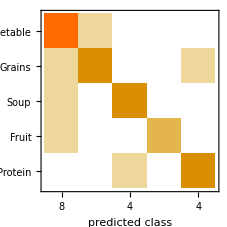
Classifier Measurements
Classifier method | Net
Number of test examples | 22
Accuracy | (73.10.) %
Accuracy baseline | (27.10.) %
Geometric mean of probabilities | 0.427 ± 0.14
Mean cross entropy | 0.851 ± 0.32
Single evaluation time | 54.5 ms/example
Batch evaluation speed | 15.6 examples/s
-Graphics- |

```mathematica
ClassifierMeasurements[trainedPretrainedNet,testData]
```

#### Example Predictions

```mathematica
(*Evaluate the model on the test data*)
predictedLabels=trainedBergNetWithoutAug[Keys[testData]];
(*Get the actual labels from the test data*)actualLabels=Values[testData];

(*Get the images from the test data*)
testImages=Keys[testData];

(*Create a list of results with images,predicted labels,and actual labels*)
results=Transpose[{testImages,predictedLabels,actualLabels}];

(*Take only 5 results*)limitedResults=RandomSample[results,5];

(*Display the results with images,predicted labels,and actual labels*)
Grid[Prepend[limitedResults,{"Image","Predicted Label","Actual Label"}],Frame->All,Spacings->{2,2}]
```

Image | Predicted Label | Actual Label
-Graphics- | Soup | Vegetable
-Graphics- | Grains | Protein
-Graphics- | Fruit | Fruit
-Graphics- | Soup | Vegetable
-Graphics- | Soup | Soup

## Results

Provided is a summary of past results in a table format. These results will be customized to what you have evaluated.

### Summary of Results

```mathematica
(*Define headers*)headers={"Model","Test Accuracy"};

(*Define the data*)
data={{"BergNet without Training",zeroShotAccuracy},{"BergNet",bergAccuracy},{"BergNet without Data Augmentation",bergNoAugmentationAccuracy},{"EfficientNet without Fine-tuning",zeroShotPretrainedAccuracy},{"Fine-tuned EfficientNet",pretrainedAccuracy}};

(*Generate the table and prepend headers*)
Grid[Prepend[data,headers],Frame->All,Spacings->{2,1},Background->{{LightGray,None}},Alignment->Center,ItemStyle->{FontFamily->"Arial",FontSize->14}]
```

Model | Test Accuracy
BergNet without Training | 0.181818
BergNet | 0.636364
BergNet without Data Augmentation | 0.454545
EfficientNet without Fine-tuning | 0.136364
Fine-tuned EfficientNet | 0.727273

## Results on Thursday Data

I returned to the dining hall on Thursday to capture another set of food images, collecting 20 new photos that will serve as an alternative test set. This additional test set allows us to assess how well our models generalize when exposed to food from a different day, which may have slight variations in appearance, lighting, or presentation. By evaluating the models on this new set, we can gauge their robustness and ability to handle subtle differences in the data, which is crucial for real-world applications where conditions are rarely identical to those in the original training environment.

### Prepare Thursday Data

```mathematica
thursdata={{"IMG_6304.HEIC","Fruit"},{"IMG_6305.HEIC","Fruit"},{"IMG_6306.HEIC","Fruit"},{"IMG_6307.HEIC","Fruit"},{"IMG_6308.HEIC","Fruit"},{"IMG_6309.HEIC","Fruit"},{"IMG_6310.HEIC","Grains"},{"IMG_6311.HEIC","Soup"},{"IMG_6312.HEIC","Soup"},{"IMG_6313.HEIC","Grains"},{"IMG_6314.HEIC","Vegetable"},{"IMG_6315.HEIC","Grains"},{"IMG_6316.HEIC","Vegetable"},{"IMG_6317.HEIC","Protein"},{"IMG_6318.HEIC","Grains"},{"IMG_6319.HEIC","Protein"},{"IMG_6320.HEIC","Grains"},{"IMG_6321.HEIC","Protein"},{"IMG_6322.HEIC","Protein"},{"IMG_6323.HEIC","Grains"}}
```

{{IMG_6304.HEIC,Fruit},{IMG_6305.HEIC,Fruit},{IMG_6306.HEIC,Fruit},{IMG_6307.HEIC,Fruit},{IMG_6308.HEIC,Fruit},{IMG_6309.HEIC,Fruit},{IMG_6310.HEIC,Grains},{IMG_6311.HEIC,Soup},{IMG_6312.HEIC,Soup},{IMG_6313.HEIC,Grains},{IMG_6314.HEIC,Vegetable},{IMG_6315.HEIC,Grains},{IMG_6316.HEIC,Vegetable},{IMG_6317.HEIC,Protein},{IMG_6318.HEIC,Grains},{IMG_6319.HEIC,Protein},{IMG_6320.HEIC,Grains},{IMG_6321.HEIC,Protein},{IMG_6322.HEIC,Protein},{IMG_6323.HEIC,Grains}}

```mathematica
imagedirectory2=currentDirectory<>"data/raw-data-thursday/";
```

```mathematica
thurspaths=thursdata[[All,1]];
thursfullPaths=FileNameJoin[{imagedirectory2,#}]&/@thurspaths;
```

```mathematica
thursimages=Import/@thursfullPaths;
```

```mathematica
Print["Number of Thursday Images: ",Length[thursimages]]
thursresizedimages=ImageResize[#,{224,224}]&/@thursimages;
```

Number of Thursday Images:20

```mathematica
thursnewMatrix=Transpose[Join[Transpose[thursdata],{thursresizedimages}]];
```

```mathematica
thursTestData=Rule@@@thursnewMatrix[[All,{3,2}]];
```

```mathematica
Print["Example of Thursday Data: ", RandomSample[thursTestData,5]]
```

Example of Thursday Data: {-Graphics-→Soup,-Graphics-→Fruit,-Graphics-→Protein,-Graphics-→Fruit,-Graphics-→Fruit}

### Evaluate Models

#### Summary of Results

```mathematica
(*Define headers*)headers2={"Model","Test Accuracy", "Thursday Test Accuracy"};
bergAccuracy2 = NetMeasurements[trainedBergNet,thursTestData,"Accuracy"];
pretrainedAccuracy2 = NetMeasurements[trainedPretrainedNet,thursTestData,"Accuracy"];
bergNoAugmentationAccuracy2 = NetMeasurements[trainedBergNetWithoutAug,thursTestData,"Accuracy"];
zeroShotAccuracy2 = NetMeasurements[initializedBergNet,thursTestData,"Accuracy"];
zeroShotPretrainedAccuracy2 = NetMeasurements[initializedPretrainedNet,thursTestData,"Accuracy"];

(*Define the data*)
data2={{"BergNet without Training",zeroShotAccuracy,zeroShotAccuracy2},{"BergNet",bergAccuracy,bergAccuracy2},{"BergNet without Data Augmentation",bergNoAugmentationAccuracy,bergNoAugmentationAccuracy2},{"EfficientNet without Fine-tuning",zeroShotPretrainedAccuracy,zeroShotPretrainedAccuracy2},{"Fine-tuned EfficientNet",pretrainedAccuracy,pretrainedAccuracy2}};

(*Generate the table and prepend headers*)
Grid[Prepend[data2,headers2],Frame->All,Spacings->{2,1},Background->{{LightGray,None}},Alignment->Center,ItemStyle->{FontFamily->"Arial",FontSize->14}]
```

Model | Test Accuracy | Thursday Test Accuracy
BergNet without Training | 0.181818 | 0.25
BergNet | 0.636364 | 0.4
BergNet without Data Augmentation | 0.454545 | 0.25
EfficientNet without Fine-tuning | 0.136364 | 0.35
Fine-tuned EfficientNet | 0.727273 | 0.7

#### More Detailed Results for BergNet and EfficientNet

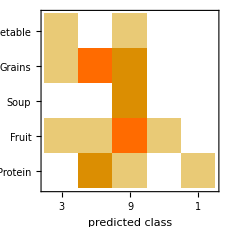
Classifier Measurements
Classifier method | Net
Number of test examples | 20
Accuracy | (40.11.) %
Accuracy baseline | (30.11.) %
Geometric mean of probabilities | 0.229 ± 0.055
Mean cross entropy | 1.47 ± 0.24
Single evaluation time | 7.81 ms/example
Batch evaluation speed | 165. examples/s
-Graphics- |

```mathematica
ClassifierMeasurements[trainedBergNet,thursTestData]
```

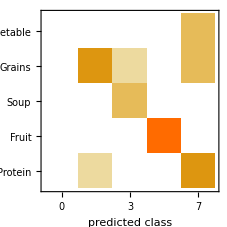
Classifier Measurements
Classifier method | Net
Number of test examples | 20
Accuracy | (70.11.) %
Accuracy baseline | (30.11.) %
Geometric mean of probabilities | 0.262 ± 0.15
Mean cross entropy | 1.34 ± 0.55
Single evaluation time | 70.6 ms/example
Batch evaluation speed | 22.4 examples/s
-Graphics- |

```mathematica
ClassifierMeasurements[trainedPretrainedNet,thursTestData]
```

## Analysis

### Predictions of Fine-tuned EfficientNet on Thursday Data

Our best-performing model, EfficientNet, also showed very high capability to generalize to new data that does not directly correlate with its training data. We found that it primarily correctly classified “everyday foods,” foods which were found on both Wednesday and Thursday in the dining hall. This makes sense since it had already been trained on similar pictures. Examples of these foods are apples, rice, noodles, and cookies, which it predicted correctly. If we search through the original data, we can find similar images as the ones shown below in the Thursday test data.

```mathematica
(*Evaluate the model on the test data*)
predictedLabels=trainedBergNetWithoutAug[Keys[thursTestData]];
(*Get the actual labels from the test data*)actualLabels=Values[thursTestData];

(*Get the images from the test data*)
testImages=Keys[thursTestData];

(*Create a list of results with images,predicted labels,and actual labels*)
results=Transpose[{testImages,predictedLabels,actualLabels}];

(*Display the results with images,predicted labels,and actual labels*)
Grid[Prepend[results,{"Image","Predicted Label","Actual Label"}],Frame->All,Spacings->{2,2}]
```

Image | Predicted Label | Actual Label
-Graphics- | Soup | Fruit
-Graphics- | Protein | Fruit
-Graphics- | Grains | Fruit
-Graphics- | Soup | Fruit
-Graphics- | Fruit | Fruit
-Graphics- | Fruit | Fruit
-Graphics- | Grains | Grains
-Graphics- | Protein | Soup
-Graphics- | Soup | Soup
-Graphics- | Fruit | Grains
-Graphics- | Grains | Vegetable
-Graphics- | Soup | Grains
-Graphics- | Vegetable | Vegetable
-Graphics- | Soup | Protein
-Graphics- | Protein | Grains
-Graphics- | Grains | Protein
-Graphics- | Vegetable | Grains
-Graphics- | Soup | Protein
-Graphics- | Soup | Protein
-Graphics- | Soup | Grains

### Case Studies

While the first image is of cheese, which is labeled as soup. The second image is of carrots, which is labeled as vegetables. However, the task is evidently difficult since there is little to distinguish the two.

```mathematica
trainedPretrainedNet[-Graphics-,{"TopProbabilities", 3}]
```

{Fruit→0.00119143,Soup→0.0524874,Vegetable→0.945291}

```mathematica
trainedPretrainedNet[-Graphics-,{"TopProbabilities", 3}]
```

While these two images are both labeled soup, the pretrained model got the redder one incorrect as vegetable and the second one correct as soup. This may be because of the brighter color of the first one. This shows how the system has discrepancies and biases likely due to overfitting on limited training data.

```mathematica
trainedPretrainedNet[-Graphics-,{"TopProbabilities",3}]
```

{Vegetable→0.148721,Grains→0.349892,Soup→0.412876}

```mathematica
trainedPretrainedNet[-Graphics-,{"TopProbabilities",3}]
```

{Vegetable→0.148721,Grains→0.349892,Soup→0.412876}

## Conclusion

In conclusion, my project, “BergNet: A Food Classification Neural Network for Custom Harvard Dining Hall Data,” demonstrates the effectiveness of neural networks in classifying food items within a unique and limited dataset. While my fine-tuned EfficientNet model outperformed BergNet and achieved 73%,  it is noteworthy that BergNet achieved significant performance levels despite being trained on only 765 images. The incorporation of data augmentation techniques proved instrumental in enhancing model performance, resulting in an increase from 45% to 63%. Additionally, my fine-tuned EfficientNet model generalized exceptionally well to images from a different day, achieving a similarly high accuracy of 70%. Overall, I found data augmentation and fine-tuning serve as effective methods in working with low amounts of data. Furthermore, the more consistent the food served at Annenberg, the better BergNet performs. These findings not only provide a roadmap for developing a custom Mathematica-based neural network tailored to a low-resource dataset but also hold the potential to enhance the dining experience for Harvard students at Annenberg Hall.